```mathematica
Grid[Partition[Tooltip[Show[ColorConvert[ColorData[#,"Image"],"RGB"],ImageSize->200],#]&/@ColorData["Gradients"],4,4,1,{}],Spacings->.5]
```

```mathematica
ic[x_]:={1/2 1/(2Zeta[3])(x/2)^2/(Exp[x/2]-1),1/8 Boole[1<x<9],1/2 x^2/Exp[x]}[[1]]
```

```mathematica
color="CMYKColors";
```

```mathematica
ColorConvert[ColorData[color,"Image"],"Grayscale"]
```

-Graphics-

```mathematica
tryCD[s_]:=If[DirectoryQ[s],SetDirectory[s],];tryCD["/home/kasper/Documents/KULeuven/PhD/Photon diffusion"];tryCD["/localhome/u0131889/Dropbox/Documents/KULeuven/PhD/Photon diffusion"];
(*tryCD["/home/user/u0131889/Nextcloud/Reset data"]*)
```

```mathematica
dir="./data-kompaneets";
```

```mathematica
Monitor[dataraw={};Do[
AppendTo[dataraw, Import[i]]
,{i,FileNames[dir<>"/hist*dat"]}],i];
Monitor[nraw={};Do[
AppendTo[nraw, Import[i]]
,{i,FileNames[dir<>"/occu*dat"]}],i];Length[dataraw]
```

63

```mathematica
data=dataraw[[-1]];
```

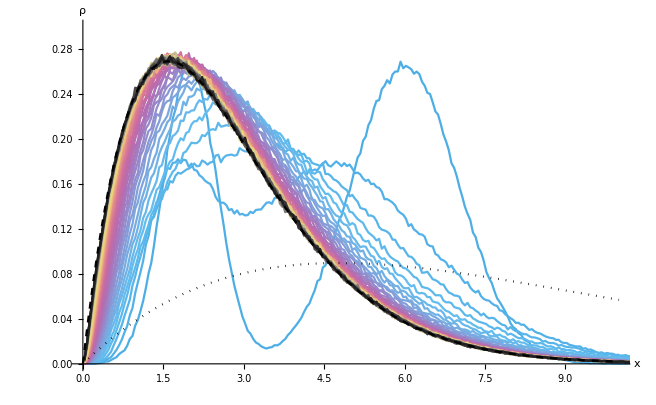

```mathematica
μ=0;kompplot=Show[
ListPlot[Mean/@Partition[#,1]&/@dataraw,PlotRange->{{0,10},{0,0.3}},Joined->True,Ticks->{Automatic,None},AxesLabel->{"x","ρ"},PlotMarkers->None,PlotStyle->ColorData["CMYKColors"]/@Range[0,1,1/(Length[dataraw]-1)]
],
Plot[{1/(2PolyLog[3,Exp[-μ]])x^2/(Exp[x+μ]-1),1/(2Zeta[3])1/3(x/3)^2/(Exp[x/3]-1)},{x,0,10},PlotTheme->"Monochrome",PlotStyle->{Dashed,Dotted},PlotRange->All,Exclusions->None]
]
```

```mathematica
Export["kompaneets-plot.pdf",kompplot]
```

```mathematica
sol=NDSolveValue[{D[ρ[t,x],t]==-D[((4x - x^2(1+2Zeta[3] ρ[t,x]/x^2)))ρ[t,x],x]+D[x^2 ρ[t,x],x,x],
ρ[0,x]==1/3 1/(√(2π (1/2)^2))Exp[-2^2(x-2)^2/2]+2/3 1/(√(2π))Exp[(-(x-6)^2)/2],ρ[t,0.001]==0,ρ[t,20]==0},
ρ,{x,0.001,20},{t,0,10}]
```

InterpolatingFunction[…]

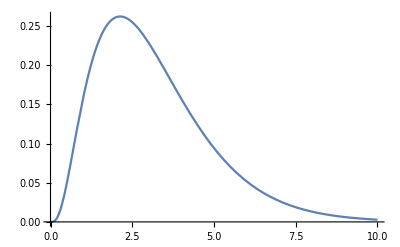

```mathematica
Plot[sol[0.5,x],{x,0.001,10}]
```

```mathematica
evolutionplot1=Show[
ListPlot[dataraw[[{2,11,101}]],PlotRange->{{0,10},{0,0.3}},Joined->True,Ticks->{Automatic,None},AxesLabel->{"x","ρ"},PlotMarkers->None,PlotTheme->"Monochrome",PlotStyle->{Dotted,Dashed,Dashing[{}]}
](*,
Plot[{sol[0.5,x]},{x,0.001,10},PlotTheme->"Monochrome",PlotStyle->{Dashed,Dotted},PlotRange->All,Exclusions->None]*)
]
```

Part::partw: Part {2,11,101} of {{{0.025,0.00028},{0.075,0.00026},{0.125,0.00026},{0.175,0.00026},{0.225,0.00036},{0.275,0.0005},{0.325,0.00084},{0.375,0.00122},{0.425,0.00198},{0.475,0.00212},«391»},{{0.025,0.0002},{0.075,0.00018},{0.125,0.00024},{0.175,0.00026},{0.225,0.00042},{0.275,0.00078},{0.325,0.00098},{0.375,0.00164},{0.425,0.00302},{0.475,0.0045},«391»},«8»,«53»} does not exist.

Part::pkspec1: The expression True cannot be used as a part specification.

ListPlot::lpn: {{{0.025,0.00028},{0.075,0.00026},{0.125,0.00026},{0.175,0.00026},{0.225,0.00036},{0.275,0.0005},{0.325,0.00084},{0.375,0.00122},{0.425,0.00198},{0.475,0.00212},«391»},{{0.025,0.0002},{0.075,0.00018},{0.125,0.00024},{0.175,0.00026},{0.225,0.00042},{0.275,0.00078},{0.325,0.00098},{0.375,0.00164},{0.425,0.00302},{0.475,0.0045},«391»},«8»,«53»}⟦{2,11,101}⟧ is not a list of numbers or pairs of numbers.

Show::gtype: ListPlot is not a type of graphics.

Show[ListPlot[1]]
 |  |  |  |

```mathematica
Export["evolution-plot-process.pdf",evolutionplot1]
```

evolution-plot-process.pdf

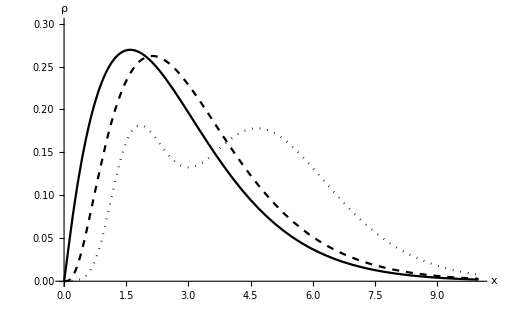

```mathematica
evolutionplot2=
Plot[Evaluate[sol[#,x]&/@{0.05,0.5,5}],{x,0.001,10},PlotRange->{{0,10},{0,0.3}},Ticks->{Automatic,None},AxesLabel->{"x","ρ"},PlotTheme->"Monochrome",PlotStyle->{Dotted,Dashed,Dashing[{}]}]
```

```mathematica
Export["evolution-plot-numerical.pdf",evolutionplot2]
```

evolution-plot-numerical.pdf

```mathematica
xsraw=Import[dir<>"/xs.dat","List"]
```

```mathematica
{bins2,counts}=HistogramList[xsraw,{Range[0,0.1,0.005]~Join~Rest@Range[0.1,20,0.05]},"PDF"];bins=MovingAverage[bins2,2];data=Transpose[{bins,counts}];
```

```mathematica
filename=Import[dir<>"/params.txt"]
```

N-1e6.00_t-20_ic-boltzmann_reset_rate-0.0013_divisor-160.00

```mathematica
data2=dataraw[[-1]];
```

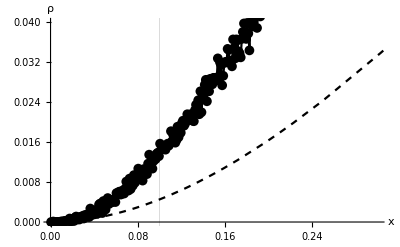

```mathematica
μ=0;histplot=Show[
ListPlot[{data},PlotRange->{{0,0.3},{0,0.04}},Joined->{True,True},Ticks->{Automatic,None},AxesLabel->{"x","ρ"},PlotStyle->Black,GridLines->{{0.1},{}},PlotMarkers->{{Automatic, Medium}}
],
Plot[{If[True,1/2 x^2/Exp[x],1/(2PolyLog[3,Exp[-μ]])x^2/(Exp[x+μ]-1)],1/(2Zeta[3]Z[b,k,c])x^2/(Exp[h[x]]-1)},{x,0,10},PlotTheme->"Monochrome",PlotStyle->{Dashed,Dotted},PlotRange->All,Exclusions->None]
]
```

```mathematica
Export["spd_"<>filename<>".pdf",histplot];
```

```mathematica
Clear[plot];plot[r_,d_]:=plot[r,d]=Module[{dir,xsraw,bins,bins2,counts,filename,μ,histplot},
dir="data-r-"<>ToString[r]<>"-d-"<>ToString[d];
xsraw=Import[dir<>"/xs.dat","List"];
{bins2,counts}=HistogramList[xsraw,{Range[0,0.1,0.005]~Join~Rest@Range[0.1,10,0.05]},"PDF"];bins=MovingAverage[bins2,2];data=Transpose[{bins,counts}];
filename=Import[dir<>"/params.txt"];
μ=0.081129;μ=0;histplot=Show[
ListPlot[{data},PlotRange->{{0,0.2},{0,0.10}},Joined->{True,True},Ticks->{Automatic,None},AxesLabel->{"x","ρ"},PlotStyle->Black,GridLines->{{0.1},{}},PlotMarkers->None,Epilog->{ Text["r="<>ToString[(1.0*^-5 2^r)]<>", d="<>ToString[10 2^d],{0.05,0.08}]}
],
Plot[{If[False,1/2 x^2/Exp[x],1/(2PolyLog[3,Exp[-μ]])x^2/(Exp[x+μ]-1)]},{x,0,10},PlotTheme->"Monochrome",PlotStyle->{Dashed,Dotted},PlotRange->All,Exclusions->None]
];
histplot]
```

```mathematica
Monitor[c=Grid[Table[plot[a,b], {a,1,9},{b,1,10}]],{a,b}]
```

```mathematica
Export["c.pdf",c]
```

c.pdf

InterpolatingFunction::dmval: Input value {0.5,20.025} lies outside the range of data in the interpolating function. Extrapolation will be used.

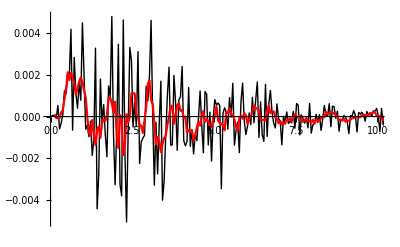

```mathematica
excess={#[[1]],#[[2]]-sol[0.5,#[[1]]](*1/(2PolyLog[3,Exp[-μ]])(#[[1]])^2/(Exp[#[[1]]+μ]-1)*)}&/@dataraw[[11]];excessplot=ListPlot[{excess,MovingAverage[excess,5]},Joined->True,PlotStyle->{{Thin,Black},Red},PlotRange->{{0,10},All}]
```

```mathematica
Export["excess_"<>filename<>".pdf", excessplot];
```

```mathematica
ndata=nraw[[-1;;]];
```

```mathematica
n2=Table[{ndata[[1,i,1]],Mean[ndata[[;;,i,2]]]},{i,20*20}];
```

```mathematica
tplot=Show[
ListPlot[Last@TakeList[{#[[1]],(#[[1]]+μ)/Log[1+1/(#[[2]])]}&/@(n2[[1;;10*20]]),{0,All}],PlotRange->{{0,0.5},All},Joined->{True,False},PlotTheme->"Monochrome",AxesLabel->{"x","T_eff"},PlotMarkers->None]]
```

```mathematica
rates={0.01,0.02,0.05,0.10,0.20,0.50,1.00};divisors={25,50,100,200};
```

```mathematica
nearZeroEstimate=Table[{r,√(r/(2Zeta[3]))},{r,rates}]
```

{{0.01,0.0644945},{0.02,0.091209},{0.05,0.144214},{0.1,0.203949},{0.2,0.288428},{0.5,0.456045},{1.,0.644945}}

```mathematica
nearZeroEstimate~Join~nearzerosR
```

{{0.01,0.0644945},{0.02,0.091209},{0.05,0.144214},{0.1,0.203949},{0.2,0.288428},{0.5,0.456045},{1.,0.644945},{{0.01,0.05209},{0.02,0.07633},{0.05,0.12693},{0.1,0.18411},{0.2,0.26968},{0.5,0.41837},{1.,0.53152}},{{0.01,0.05984},{0.02,0.08482},{0.05,0.137},{0.1,0.1934},{0.2,0.28144},{0.5,0.43342},{1.,0.6146}},{{0.01,0.06097},{0.02,0.08667},{0.05,0.1391},{0.1,0.19836},{0.2,0.28055},{0.5,0.44039},{1.,0.62085}},{{0.01,0.06024},{0.02,0.08417},{0.05,0.13136},{0.1,0.19029},{0.2,0.27006},{0.5,0.42518},{1.,0.60517}}}

```mathematica
DisplayForm[SqrtBox[r/(2Zeta[3])]]
```

√(r/(2 Zeta[3]))

```mathematica
nearzerosR=Table[{r,
1/10000000 1/0.01 ToExpression@Import["data-alot-r-"<>ToString[NumberForm[r,{3,2}]]<>"-d-"<>ToString[d]<>"/nearzero.txt"]},{d,divisors},{r,rates}];
```

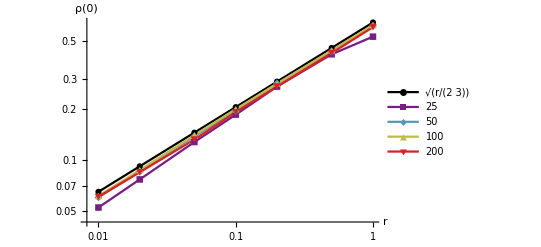

```mathematica
nearplotR=ListLogLogPlot[{nearZeroEstimate}~Join~nearzerosR,Joined->True,PlotLegends->{DisplayForm@SqrtBox[r/(2Zeta[3])]}~Join~Table[d,{d,divisors}],PlotStyle->{Black}~Join~(ColorData["Rainbow"]/@Range[0,1,1/(Length[divisors]-1)]),AxesLabel->{"r","ρ(0)"},PlotMarkers->Automatic]
```

```mathematica
Export["near-divisors.pdf",nearplotR]
```

near-divisors.pdf

```mathematica
NIntegrate[1/(2Zeta[3])x^2/(Exp[x]-1),{x,0,0.01}]
```

0.0000207284

```mathematica
FindFit[nearzerosR[[4]],(a)(x/(2Zeta[3]))^(1/2),{{a,1}},x]
```

{a→0.935316}

```mathematica
1/(2Zeta[3])//N
```

0.415954

```mathematica
0.14^2
```

0.0196

```mathematica
Sqrt[1/(2Zeta[3])]//N
```

0.644945

```mathematica
nearzerosD=Table[{d,
ToExpression@Import["data-alot-r-"<>ToString[NumberForm[r,{3,2}]]<>"-d-"<>ToString[d]<>"/nearzero.txt"]},{r,rates},{d,divisors}];
```

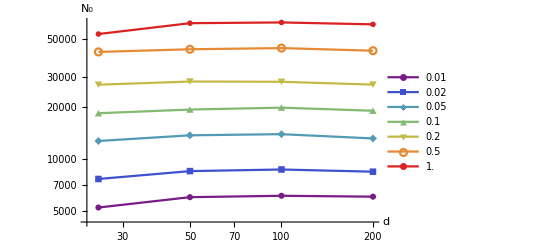

```mathematica
nearplotD=ListLogLogPlot[nearzerosD,Joined->True,PlotLegends->Table[r,{r,rates}],PlotStyle->(ColorData["Rainbow"]/@Range[0,1,1/(Length[rates]-1)]),AxesLabel->{"d","N_0"},PlotMarkers->Automatic]
```

```mathematica
Export["near-rates.pdf",nearplotD]
```

near-rates.pdf

```mathematica
nearzeros=Table[{d,r,ToExpression@Import["data-alot-r-"<>ToString[NumberForm[r,{3,2}]]<>"-d-"<>ToString[d]<>"/nearzero.txt"]},{d,divisors},{r,rates}];
```

Import::nffil: File data-alot-r-1.00-d-25/nearzero.txt not found during Import.

Import::nffil: File data-alot-r-0.01-d-200/nearzero.txt not found during Import.

```mathematica
nearzeros
```

```mathematica
hist=Import["data-alot-r-0.01-d-25/hist001000.dat"]
```

{{0.0005,0.0507},{0.0015,0.051},{0.0025,0.0527},{0.0035,0.0493},{0.0045,0.0509},{0.0055,0.0543},{0.0065,0.0524},{0.0075,0.0511},{0.0085,0.0531},{0.0095,0.0554},{0.0105,0.0532},{0.0115,0.0558},{0.0125,0.0524},{0.0135,0.0568},{0.0145,0.0522},19971,{19.9865,0.},{19.9875,0.},{19.9885,0.},{19.9895,0.},{19.9905,0.},{19.9915,0.},{19.9925,0.},{19.9935,0.},{19.9945,0.},{19.9955,0.},{19.9965,0.},{19.9975,0.},{19.9985,0.},{19.9995,0.},{20.0005,0.}}
 |  |  |  |

```mathematica
hists=Table[Import["data-alot-r-"<>ToString[NumberForm[0.10,{3,2}]]<>"-d-"<>ToString[d]<>"/hist001000.dat"],{d,divisors}];
```

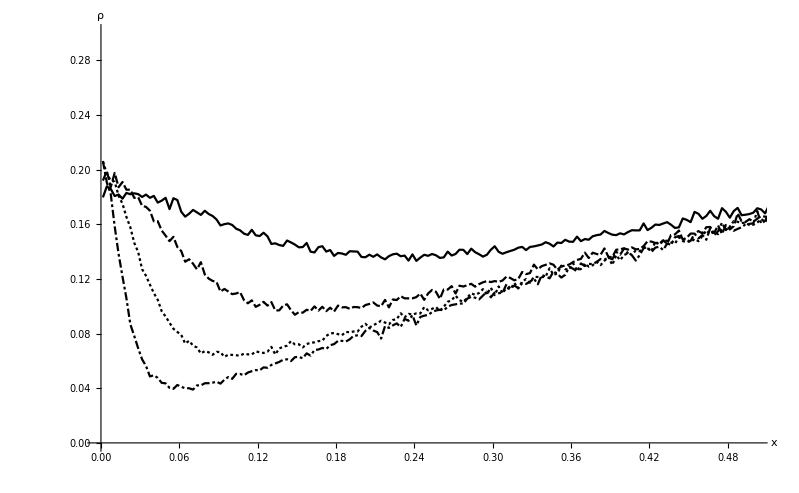

```mathematica
zoomplot=ListPlot[Mean/@Partition[#,3]&/@hists,PlotRange->{{0,0.5},{0,0.3}},Joined->True,PlotTheme->"Monochrome",PlotMarkers->None,Ticks->{Automatic,Automatic},AxesLabel->{"x","ρ"}]
```

```mathematica
0.10^2/(2Zeta[3])
```

0.00415954

```mathematica
Export["zoomplot-r002.pdf",zoomplot]
```

zoomplot-r002.pdf

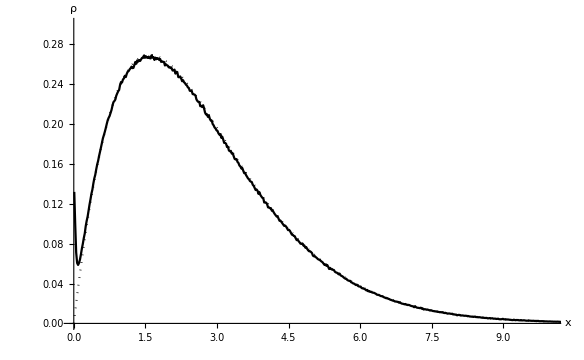

```mathematica
μ=0;fullplot=Show[
ListPlot[Take[First@hists,0]~Join~(Mean/@Partition[Drop[First@hists,0],20]),PlotRange->{{0,10},{0,0.3}},Joined->True,PlotTheme->"Monochrome",PlotMarkers->None,Ticks->{Automatic,None},AxesLabel->{"x","ρ"}]
,
Plot[{1/(2PolyLog[3,Exp[-μ]])x^2/(Exp[x+μ]-1)},{x,0,10},PlotTheme->"Monochrome",PlotStyle->{Dashed,Dotted},PlotRange->All,Exclusions->None]]
```

```mathematica
Export["fullplanck.pdf",fullplot]
```

fullplanck.pdf

```mathematica
Export["temp_" <> filename <> ".pdf", tplot]
```

```mathematica
ns=Import["data/n.dat"];
```

```mathematica
nplot=Show[
ListPlot[ns[[;;;;100]],PlotLegends->Automatic,Joined->True,PlotRange->All],
Plot[{Z[b,k,c]},{x,0,1000},PlotTheme->"Monochrome"]
]
```

```mathematica
Export["n "<>filename<>".pdf",nplot];
```

```mathematica
c=1/100;b=00/100;k=4/10;
```

```mathematica
x0=1/10;
```

```mathematica
h[x_]:=NIntegrate[Piecewise[{{1,s<=x0},{1+b s^k,s>x0}}]/(1+Piecewise[{{0,s<=x0},{c/s^3,s>x0}}]),{s,0,x}]
```

```mathematica
Clear[Z];Z[b_,k_,c_]:=Z[b,k,c]=Module[{h2},
h2[x_]:=NIntegrate[Piecewise[{{1,s<=x0},{1+b s^k,s>x0}}]/(1+Piecewise[{{0,s<=x0},{c/s^3,s>x0}}]),{s,0,x}];
NIntegrate[1/(2Zeta[3])xx^2/(Exp[h2[xx]]-1),{xx,0,∞}]]
```

```mathematica
plot=histplot=Show[
ListPlot[data2,PlotRange->{{0,10},All},Joined->True,PlotStyle->Table[ColorData[color,i/(Length[data]-1)],{i,0,Length[data]-1}],(*PlotLegends->BarLegend[{"CMYKColors",{0,2}}],*)Ticks->{Automatic,None},AxesLabel->{"x","ρ"}
],
Plot[{1/(2Zeta[3])x^2/(Exp[x]-1)(*,1/(2Zeta[3]Z[b,k,c])x^2/(Exp[h[x]]-1)*)},{x,0,10},PlotTheme->"Monochrome",PlotStyle->{Dotted},PlotRange->All,Exclusions->None]
]
```

```mathematica
Export["compare " <>filename<>".pdf",pplot]
```

compare N-1e5.70 dx-0.05 t-100 dt-0.0001 ic-planck c-0.1000 brems.pdf

```mathematica
Plot[{1/QPochhammer[-k^2,1/100],1/QPochhammer[-(k/10)^2,1/100](1+k^2)^-1},{k,-10,+10},PlotRange->All]
```

```mathematica
Product[1/(1+(k/10^m)^2)1/10^m,{m,0,∞}]
```

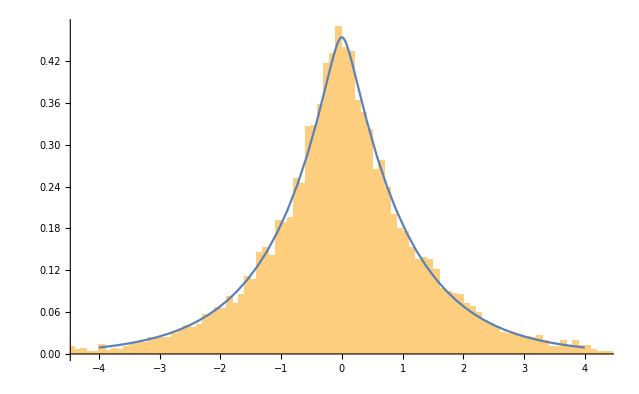

```mathematica
Show[
Histogram[a,{0.1},"PDF"],
Plot[f[x],{x,-4,+4}]]
```